Shapefiles downloaded from: https://www.census.gov/cgi-bin/geo/shapefiles/

```mathematica
mapDir=FileNameJoin[{NotebookDirectory[],"shapefiles"}];
```

```mathematica
districts=Import[FileNameJoin[{mapDir,"tl_2025_17_cd119.zip"}],{"SHP","Data"}][[1,2,2]];
districts=Most[districts];(*The last one appears to just be water in Lake Michigan*)
```

```mathematica
districtColors=FindVertexColoring[AdjacencyGraph@Boole@Outer[Not@*DisjointQ,districts[[All,1,1]],districts[[All,1,1]],1],ColorData[116,"ColorList"]];
```

```mathematica
tracts=Import[FileNameJoin[{mapDir,"tl_2025_17_tract.zip"}],{"SHP","Data"}][[1,2,2]];
```

```mathematica
blocks=Import[FileNameJoin[{mapDir,"tl_2025_17_tabblock20.zip"}],{"SHP","Data"}][[1,2,2]];
```

```mathematica
GeoGraphics[{
GeoStyling[Opacity[1]],
Transpose[{districtColors,districts}]
}
]//EchoTiming
```

2.17683

-Graphics-

```mathematica
nf=Nearest@Catenate[MapIndexed[Thread[Cases[#1,{_Real,_Real},Infinity]->First[#2]]&,blocks]]
```

NearestFunction[{2, <>}]

```mathematica
(*center=GeoPosition[{41.795108,-87.594540}];*)
center=GeoPosition[{41.795108,-87.6}];
map=GeoGraphics[{
GeoStyling[Opacity[1]],
Transpose[{districtColors,districts}],
{FaceForm[],EdgeForm[Directive[Thickness[0.002],Black]],blocks[[Union@nf[center[[1]],25000]]]},
{FaceForm[],EdgeForm[Directive[Thickness[0.0035],StandardRed]],tracts}
},
GeoRange->Quantity[1.3,"Miles"],
GeoCenter->center,
AspectRatio->1/GoldenRatio,
(*GeoBackground->"VectorMinimalNoLabels"*)
GeoBackground->LightBlue,
ImageSize->600
]//EchoTiming
```

3.84394

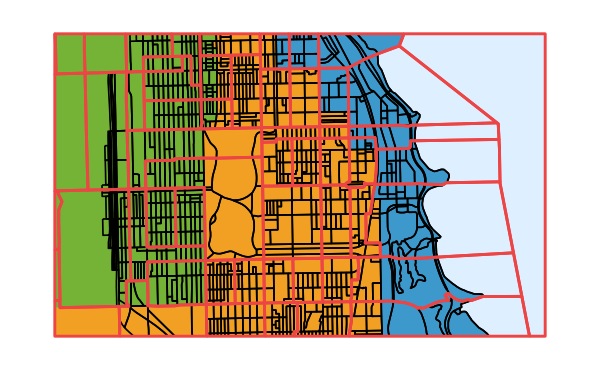

```mathematica
Export["~/git/overleaf/CVAP/figs/blockTractMap2.pdf",map];
Export["~/git/overleaf/CVAP/figs/blockTractMap2.png",map,RasterSize->1000];
```